```mathematica
D[x^2+8xy+3 y^8-Sin[8xy],x]
```

2 x

```mathematica
D[x^2+8xy+3 y^8-Sin[8xy],y]
```

24 y^7

```mathematica
D[ArcTan[(8x)/y],x]
```

8/((1+(64 x^2)/y^2) y)

```mathematica
D[ArcTan[(8x)/y],y]
```

-(8 x)/((1+(64 x^2)/y^2) y^2)

```mathematica
D[(x+8y)/(√(x^2+y^2)),x]
```

-(x (x+8 y))/((x^2+y^2)^(3/2))+1/(√(x^2+y^2))

```mathematica
D[(x+8y)/(√(x^2+y^2)),y]
```

-(y (x+8 y))/((x^2+y^2)^(3/2))+8/(√(x^2+y^2))

```mathematica
z=x^8+xy^8-5 y^8-Cos[8xy]
```

x^8+xy^8-5 y^8-Cos[8 xy]

```mathematica
D[z,{x,2}]
```

56 x^6

```mathematica
D[z,{x,1},{y,1}]
```

0

```mathematica
D[z,{y,1},{x,1}]
```

0

```mathematica
D[z,{y,2}]
```

-280 y^6

```mathematica
z=Tan[(8x)/Log[ⅇ,y]]
```

Tan[(8 x)/Log[y]]

```mathematica
D[z,{x,2}]
```

(128 Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]])/Log[y]^2

```mathematica
D[z,{x,1},{y,1}]
```

-(8 Sec[(8 x)/Log[y]]^2)/(y Log[y]^2)-(128 x Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]])/(y Log[y]^3)

```mathematica
D[z,{y,1},{x,1}]
```

-(8 Sec[(8 x)/Log[y]]^2)/(y Log[y]^2)-(128 x Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]])/(y Log[y]^3)

```mathematica
D[z,{y,2}]
```

(16 x Sec[(8 x)/Log[y]]^2)/(y^2 Log[y]^3)+(8 x Sec[(8 x)/Log[y]]^2)/(y^2 Log[y]^2)+(128 x^2 Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]])/(y^2 Log[y]^4)

```mathematica
u=(x^8-8yz+z^x)/(√(x^2+y^2-8 z^3))
```

(x^8-8 yz+Tan[(8 x)/Log[y]]^x)/(√(x^2+y^2-8 Tan[(8 x)/Log[y]]^3))

```mathematica
D[u,{x,2}]
```

-((2 x-(192 Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^2)/Log[y]) (8 x^7+(Log[Tan[(8 x)/Log[y]]]+(8 x Csc[(8 x)/Log[y]] Sec[(8 x)/Log[y]])/Log[y]) Tan[(8 x)/Log[y]]^x))/(x^2+y^2-8 Tan[(8 x)/Log[y]]^3)^(3/2)+(56 x^6+(Log[Tan[(8 x)/Log[y]]]+(8 x Csc[(8 x)/Log[y]] Sec[(8 x)/Log[y]])/Log[y])^2 Tan[(8 x)/Log[y]]^x+(-(64 x Csc[(8 x)/Log[y]]^2)/Log[y]^2+(16 Csc[(8 x)/Log[y]] Sec[(8 x)/Log[y]])/Log[y]+(64 x Sec[(8 x)/Log[y]]^2)/Log[y]^2) Tan[(8 x)/Log[y]]^x)/(√(x^2+y^2-8 Tan[(8 x)/Log[y]]^3))+(x^8-8 yz+Tan[(8 x)/Log[y]]^x) ((3 (2 x-(192 Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^2)/Log[y])^2)/(4 (x^2+y^2-8 Tan[(8 x)/Log[y]]^3)^(5/2))-(2-(3072 Sec[(8 x)/Log[y]]^4 Tan[(8 x)/Log[y]])/Log[y]^2-(3072 Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^3)/Log[y]^2)/(2 (x^2+y^2-8 Tan[(8 x)/Log[y]]^3)^(3/2)))

```mathematica
D[u,{x,1},{y,1}]
```

(4 x^2 Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^(-1+x) (2 x-(192 Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^2)/Log[y]))/(y Log[y]^2 (x^2+y^2-8 Tan[(8 x)/Log[y]]^3)^(3/2))+(3 (2 y+(192 x Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^2)/(y Log[y]^2)) (2 x-(192 Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^2)/Log[y]) (x^8-8 yz+Tan[(8 x)/Log[y]]^x))/(4 (x^2+y^2-8 Tan[(8 x)/Log[y]]^3)^(5/2))-(((3072 x Sec[(8 x)/Log[y]]^4 Tan[(8 x)/Log[y]])/(y Log[y]^3)+(192 Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^2)/(y Log[y]^2)+(3072 x Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^3)/(y Log[y]^3)) (x^8-8 yz+Tan[(8 x)/Log[y]]^x))/(2 (x^2+y^2-8 Tan[(8 x)/Log[y]]^3)^(3/2))-((2 y+(192 x Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^2)/(y Log[y]^2)) (8 x^7+(Log[Tan[(8 x)/Log[y]]]+(8 x Csc[(8 x)/Log[y]] Sec[(8 x)/Log[y]])/Log[y]) Tan[(8 x)/Log[y]]^x))/(2 (x^2+y^2-8 Tan[(8 x)/Log[y]]^3)^(3/2))+(-1/(y Log[y]^2)8 x^2 Sec[(8 x)/Log[y]]^2 (Log[Tan[(8 x)/Log[y]]]+(8 x Csc[(8 x)/Log[y]] Sec[(8 x)/Log[y]])/Log[y]) Tan[(8 x)/Log[y]]^(-1+x)+((64 x^2 Csc[(8 x)/Log[y]]^2)/(y Log[y]^3)-(16 x Csc[(8 x)/Log[y]] Sec[(8 x)/Log[y]])/(y Log[y]^2)-(64 x^2 Sec[(8 x)/Log[y]]^2)/(y Log[y]^3)) Tan[(8 x)/Log[y]]^x)/(√(x^2+y^2-8 Tan[(8 x)/Log[y]]^3))

```mathematica
D[u,{x,1},{z,1}]
```

-(x Tan[(8 x)/Log[y]]^(-1+x) (2 x-(192 Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^2)/Log[y]))/(2 (x^2+y^2-8 Tan[(8 x)/Log[y]]^3)^(3/2))+(Tan[(8 x)/Log[y]]^(-1+x)+x (Log[Tan[(8 x)/Log[y]]]+(8 x Csc[(8 x)/Log[y]] Sec[(8 x)/Log[y]])/Log[y]) Tan[(8 x)/Log[y]]^(-1+x))/(√(x^2+y^2-8 Tan[(8 x)/Log[y]]^3))-(18 Tan[(8 x)/Log[y]]^2 (2 x-(192 Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^2)/Log[y]) (x^8-8 yz+Tan[(8 x)/Log[y]]^x))/((x^2+y^2-8 Tan[(8 x)/Log[y]]^3)^(5/2))+(192 Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]] (x^8-8 yz+Tan[(8 x)/Log[y]]^x))/(Log[y] (x^2+y^2-8 Tan[(8 x)/Log[y]]^3)^(3/2))+(12 Tan[(8 x)/Log[y]]^2 (8 x^7+(Log[Tan[(8 x)/Log[y]]]+(8 x Csc[(8 x)/Log[y]] Sec[(8 x)/Log[y]])/Log[y]) Tan[(8 x)/Log[y]]^x))/(x^2+y^2-8 Tan[(8 x)/Log[y]]^3)^(3/2)

```mathematica
D[u,{y,1},{x,1}]
```

(4 x^2 Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^(-1+x) (2 x-(192 Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^2)/Log[y]))/(y Log[y]^2 (x^2+y^2-8 Tan[(8 x)/Log[y]]^3)^(3/2))-(16 x Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^(-1+x))/(y Log[y]^2 √(x^2+y^2-8 Tan[(8 x)/Log[y]]^3))-(8 x^2 Sec[(8 x)/Log[y]]^2 (Log[Tan[(8 x)/Log[y]]]+(8 (-1+x) Csc[(8 x)/Log[y]] Sec[(8 x)/Log[y]])/Log[y]) Tan[(8 x)/Log[y]]^(-1+x))/(y Log[y]^2 √(x^2+y^2-8 Tan[(8 x)/Log[y]]^3))-(128 x^2 Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^x)/(y Log[y]^3 √(x^2+y^2-8 Tan[(8 x)/Log[y]]^3))+(3 (2 y+(192 x Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^2)/(y Log[y]^2)) (2 x-(192 Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^2)/Log[y]) (x^8-8 yz+Tan[(8 x)/Log[y]]^x))/(4 (x^2+y^2-8 Tan[(8 x)/Log[y]]^3)^(5/2))-(((3072 x Sec[(8 x)/Log[y]]^4 Tan[(8 x)/Log[y]])/(y Log[y]^3)+(192 Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^2)/(y Log[y]^2)+(3072 x Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^3)/(y Log[y]^3)) (x^8-8 yz+Tan[(8 x)/Log[y]]^x))/(2 (x^2+y^2-8 Tan[(8 x)/Log[y]]^3)^(3/2))-((2 y+(192 x Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^2)/(y Log[y]^2)) (8 x^7+(Log[Tan[(8 x)/Log[y]]]+(8 x Csc[(8 x)/Log[y]] Sec[(8 x)/Log[y]])/Log[y]) Tan[(8 x)/Log[y]]^x))/(2 (x^2+y^2-8 Tan[(8 x)/Log[y]]^3)^(3/2))

```mathematica
D[u,{y,2}]
```

(8 x^2 Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^(-1+x) (2 y+(192 x Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^2)/(y Log[y]^2)))/(y Log[y]^2 (x^2+y^2-8 Tan[(8 x)/Log[y]]^3)^(3/2))+((64 (-1+x) x^3 Sec[(8 x)/Log[y]]^4 Tan[(8 x)/Log[y]]^(-2+x))/(y^2 Log[y]^4)+(16 x^2 Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^(-1+x))/(y^2 Log[y]^3)+(8 x^2 Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^(-1+x))/(y^2 Log[y]^2)+(128 x^3 Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^x)/(y^2 Log[y]^4))/(√(x^2+y^2-8 Tan[(8 x)/Log[y]]^3))+(x^8-8 yz+Tan[(8 x)/Log[y]]^x) ((3 (2 y+(192 x Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^2)/(y Log[y]^2))^2)/(4 (x^2+y^2-8 Tan[(8 x)/Log[y]]^3)^(5/2))-(2-(3072 x^2 Sec[(8 x)/Log[y]]^4 Tan[(8 x)/Log[y]])/(y^2 Log[y]^4)-(384 x Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^2)/(y^2 Log[y]^3)-(192 x Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^2)/(y^2 Log[y]^2)-(3072 x^2 Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^3)/(y^2 Log[y]^4))/(2 (x^2+y^2-8 Tan[(8 x)/Log[y]]^3)^(3/2)))

```mathematica
D[u,{y,1},{z,1}]
```

-(96 x^2 Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^(1+x))/(y Log[y]^2 (x^2+y^2-8 Tan[(8 x)/Log[y]]^3)^(3/2))-(x Tan[(8 x)/Log[y]]^(-1+x) (2 y+(192 x Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^2)/(y Log[y]^2)))/(2 (x^2+y^2-8 Tan[(8 x)/Log[y]]^3)^(3/2))-(8 (-1+x) x^2 Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^(-2+x))/(y Log[y]^2 √(x^2+y^2-8 Tan[(8 x)/Log[y]]^3))-(18 Tan[(8 x)/Log[y]]^2 (2 y+(192 x Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^2)/(y Log[y]^2)) (x^8-8 yz+Tan[(8 x)/Log[y]]^x))/((x^2+y^2-8 Tan[(8 x)/Log[y]]^3)^(5/2))-(192 x Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]] (x^8-8 yz+Tan[(8 x)/Log[y]]^x))/(y Log[y]^2 (x^2+y^2-8 Tan[(8 x)/Log[y]]^3)^(3/2))

```mathematica
D[u,{z,1},{x,1}]
```

-(x Tan[(8 x)/Log[y]]^(-1+x) (2 x-(192 Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^2)/Log[y]))/(2 (x^2+y^2-8 Tan[(8 x)/Log[y]]^3)^(3/2))+Tan[(8 x)/Log[y]]^(-1+x)/(√(x^2+y^2-8 Tan[(8 x)/Log[y]]^3))+(x (Log[Tan[(8 x)/Log[y]]]+(8 (-1+x) Csc[(8 x)/Log[y]] Sec[(8 x)/Log[y]])/Log[y]) Tan[(8 x)/Log[y]]^(-1+x))/(√(x^2+y^2-8 Tan[(8 x)/Log[y]]^3))-(18 Tan[(8 x)/Log[y]]^2 (2 x-(192 Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^2)/Log[y]) (x^8-8 yz+Tan[(8 x)/Log[y]]^x))/((x^2+y^2-8 Tan[(8 x)/Log[y]]^3)^(5/2))+(192 Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]] (x^8-8 yz+Tan[(8 x)/Log[y]]^x))/(Log[y] (x^2+y^2-8 Tan[(8 x)/Log[y]]^3)^(3/2))+(12 Tan[(8 x)/Log[y]]^2 (8 x^7+(Log[Tan[(8 x)/Log[y]]]+(8 x Csc[(8 x)/Log[y]] Sec[(8 x)/Log[y]])/Log[y]) Tan[(8 x)/Log[y]]^x))/(x^2+y^2-8 Tan[(8 x)/Log[y]]^3)^(3/2)

```mathematica
D[u,{z,1},{y,1}]
```

-(96 x^2 Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^(1+x))/(y Log[y]^2 (x^2+y^2-8 Tan[(8 x)/Log[y]]^3)^(3/2))-(x Tan[(8 x)/Log[y]]^(-1+x) (2 y+(192 x Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^2)/(y Log[y]^2)))/(2 (x^2+y^2-8 Tan[(8 x)/Log[y]]^3)^(3/2))-(8 (-1+x) x^2 Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^(-2+x))/(y Log[y]^2 √(x^2+y^2-8 Tan[(8 x)/Log[y]]^3))-(18 Tan[(8 x)/Log[y]]^2 (2 y+(192 x Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]]^2)/(y Log[y]^2)) (x^8-8 yz+Tan[(8 x)/Log[y]]^x))/((x^2+y^2-8 Tan[(8 x)/Log[y]]^3)^(5/2))-(192 x Sec[(8 x)/Log[y]]^2 Tan[(8 x)/Log[y]] (x^8-8 yz+Tan[(8 x)/Log[y]]^x))/(y Log[y]^2 (x^2+y^2-8 Tan[(8 x)/Log[y]]^3)^(3/2))

```mathematica
D[u,{z,2}]
```

(24 x Tan[(8 x)/Log[y]]^(1+x))/((x^2+y^2-8 Tan[(8 x)/Log[y]]^3)^(3/2))+((-1+x) x Tan[(8 x)/Log[y]]^(-2+x))/(√(x^2+y^2-8 Tan[(8 x)/Log[y]]^3))+(x^8-8 yz+Tan[(8 x)/Log[y]]^x) ((432 Tan[(8 x)/Log[y]]^4)/((x^2+y^2-8 Tan[(8 x)/Log[y]]^3)^(5/2))+(24 Tan[(8 x)/Log[y]])/((x^2+y^2-8 Tan[(8 x)/Log[y]]^3)^(3/2)))

```mathematica
Integrate[x^3+8x-Cos[8x]+9^x+√(8x),x]
```

4/3 √2 x^(3/2)+4 x^2+x^4/4+9^x/Log[9]-1/8 Sin[8 x]

```mathematica
Integrate[x^2 Log[ⅇ,8x],x]
```

-x^3/9+1/3 x^3 Log[8 x]

```mathematica
Integrate[ⅇ^(8x)Sin[β*x],x]
```

(ⅇ^(8 x) (-β Cos[x β]+8 Sin[x β]))/(64+β^2)

```mathematica
Integrate[(2x-1)/((8x-3)(x^2+8)),x]
```

(131 √2 ArcTan[x/(2 √2)]-8 Log[-3+8 x]+4 Log[64 (8+x^2)])/2084

```mathematica
Integrate[Sin[7x]*Cos[3x]*Sin[8x],x]
```

1/8 Sin[2 x]+1/16 Sin[4 x]-1/48 Sin[12 x]-1/72 Sin[18 x]

```mathematica
Integrate[x*Sin[8x+1],x]
```

-1/8 x Cos[1+8 x]+1/64 Sin[1+8 x]

```mathematica
Integrate[(√x)/(√x+8),x]
```

-16 √x+x+128 Log[8+√x]

```mathematica
Integrate[x^2(x^(1/3)+8)^(1/4),x]
```

1/195634725 4 (8+x^(1/3))^(1/4) (1125899906842624-35184372088832 x^(1/3)+2748779069440 x^(2/3)-257698037760 x+26172456960 x^(4/3)-2780823552 x^(5/3)+304152576 x^2-33945600 x^(7/3)+3845400 x^(8/3)+15862275 x^3)

```mathematica
Integrate[x+8 x^2+x^5,{x,1,3}]
```

584/3

```mathematica
Integrate[(√x+8)/x^2,{x,1,4}]
```

7

```mathematica
Integrate[(x^2+8x-5)*Cos[x],{x,0,π}]
```

-2 (8+π)

```mathematica
Integrate[(2x-1)/(x(8x+1)(x+8)),{x,2,3}]
```

1/504 (-63 Log[3]+177 Log[5]-80 Log[17/2]-17 Log[11])

```mathematica
Integrate[√x+8 x^3+x^8,{x,1,8}]
```

1/9 (134291431+96 √2)

```mathematica
Integrate[Log[ⅇ,8x],{x,1,ⅇ}]
```

1-Log[8]+ⅇ Log[8]

```mathematica
Integrate[(8 x^3-7)*Cos[x/2],{x,0,π/2}]
```

768-391 √2+√2 π (-96+π (12+π))

```mathematica
Integrate[x/(√(x^2+8^2)),{x,0,8}]
```

8 (-1+√2)

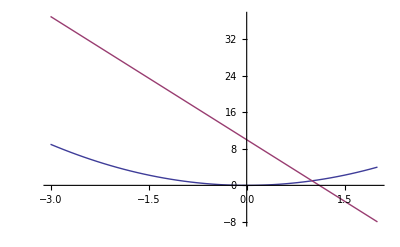

```mathematica
(*Construim domeniul*)
Plot[{x^2,10-9x},{x,-3,2}]
```

```mathematica
Solve[{y==x^2,y==10-8x},{x,y}]
```

{{y→2 (21-4 √26),x→-4+√26},{y→2 (21+4 √26),x→-4-√26}}

```mathematica
S=∫_(2 (21+4 √26))^(-4-√26) (10-8x-x^2)ⅆx
```

323380/3+21140 √26

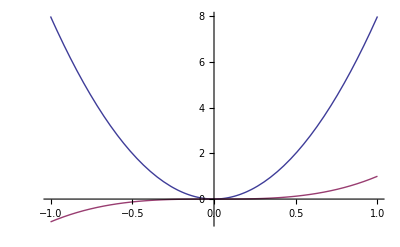

```mathematica
(*Construim domeniul*)
Plot[{8 x^2,x^3},{x,-1,1}]
```

```mathematica
Solve[{y==8 x^2,y==x^3},{x,y}]
```

{{y→0,x→0},{y→0,x→0},{y→512,x→8}}

```mathematica
S=∫_512^8 (x^3-8 x^2)ⅆx
```

-16821955584

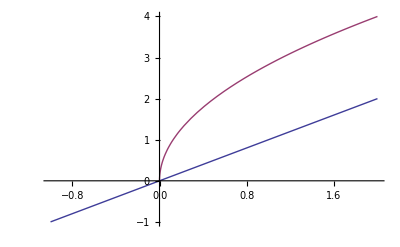

```mathematica
(*Construim domeniul*)
Plot[{x,√(8x)},{x,-1,2}]
```

```mathematica
Solve[{y==x,y==√(8x)},{x,y}]
```

{{x→0,y→0},{x→8,y→8}}

```mathematica
S=∫_8^8 (√(8x)-x)ⅆx
```

0

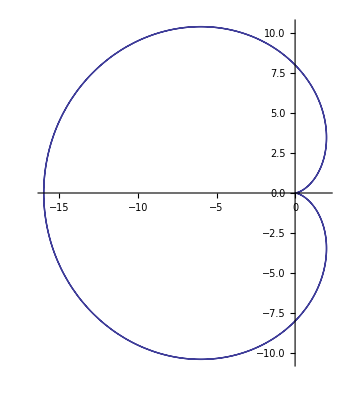

```mathematica
PolarPlot[{8-8Cos[φ]},{φ,-2Pi,2Pi}]
```

```mathematica
Solve[{y==8(1-Cos[φ])},{y}]
```

{{y→-8 (-1+Cos[φ])}}

```mathematica
S=∫_0^(8(1-Cos[φ])) 8(1-Cos[φ])ⅆy
```

64 (1-Cos[φ])^2

```mathematica
z=x^y+8 x^2*y+7 y^8
{D[z,{x,2},{y,1}],D[z,{y,1},{x,1},{y,1}]}
```

x^y+8 x^2 y+7 y^8

{16+x^(-2+y) (-1+y)+x^(-2+y) y+x^(-2+y) (-1+y) y Log[x],2 x^(-1+y) Log[x]+x^(-1+y) y Log[x]^2}

```mathematica
z=ArcTan[x^8/(8y)]
{D[z,{x,1},{y,1},{x,1}]}
```

ArcTan[x^8/(8 y)]

{-x^38/(64 (1+x^16/(64 y^2))^3 y^6)+(31 x^22)/(32 (1+x^16/(64 y^2))^2 y^4)-(7 x^6)/((1+x^16/(64 y^2)) y^2)}

```mathematica
u=(x*z^8+y^16)/(√(x^2-z*y^2))
{D[u,{x,1},{y,1},{z,3}]}
```

(y^16+x ArcTan[x^8/(8 y)]^8)/(√(x^2-y^2 ArcTan[x^8/(8 y)]))

{(-(840 x^16 ArcTan[x^8/(8 y)]^3)/((1+x^16/(64 y^2))^2 y^3)+(105 x^24 ArcTan[x^8/(8 y)]^4)/(2 (1+x^16/(64 y^2))^2 y^4)-(1890 x^8 ArcTan[x^8/(8 y)]^4)/((1+x^16/(64 y^2)) y^2))/(√(x^2-y^2 ArcTan[x^8/(8 y)]))+(3 y^2 (-(210 x^16 ArcTan[x^8/(8 y)]^4)/((1+x^16/(64 y^2))^2 y^3)+(21 x^24 ArcTan[x^8/(8 y)]^5)/(2 (1+x^16/(64 y^2))^2 y^4)-(378 x^8 ArcTan[x^8/(8 y)]^5)/((1+x^16/(64 y^2)) y^2)))/(2 (x^2-y^2 ArcTan[x^8/(8 y)])^(3/2))+(9 y^4 (-(42 x^16 ArcTan[x^8/(8 y)]^5)/((1+x^16/(64 y^2))^2 y^3)+(7 x^24 ArcTan[x^8/(8 y)]^6)/(4 (1+x^16/(64 y^2))^2 y^4)-(63 x^8 ArcTan[x^8/(8 y)]^6)/((1+x^16/(64 y^2)) y^2)))/(4 (x^2-y^2 ArcTan[x^8/(8 y)])^(5/2))+(15 y^6 (-(7 x^16 ArcTan[x^8/(8 y)]^6)/((1+x^16/(64 y^2))^2 y^3)+(x^24 ArcTan[x^8/(8 y)]^7)/(4 (1+x^16/(64 y^2))^2 y^4)-(9 x^8 ArcTan[x^8/(8 y)]^7)/((1+x^16/(64 y^2)) y^2)))/(8 (x^2-y^2 ArcTan[x^8/(8 y)])^(7/2))-1/2 (2 x-(x^7 y)/(1+x^16/(64 y^2))) (-(315 x^9 y^2 ArcTan[x^8/(8 y)]^6)/(4 (1+x^16/(64 y^2)) (x^2-y^2 ArcTan[x^8/(8 y)])^(7/2))-(189 x^9 ArcTan[x^8/(8 y)]^5)/((1+x^16/(64 y^2)) (x^2-y^2 ArcTan[x^8/(8 y)])^(5/2))-(210 x^9 ArcTan[x^8/(8 y)]^4)/((1+x^16/(64 y^2)) y^2 (x^2-y^2 ArcTan[x^8/(8 y)])^(3/2))+(105 y^6 (16 y^15-(x^9 ArcTan[x^8/(8 y)]^7)/((1+x^16/(64 y^2)) y^2)))/(8 (x^2-y^2 ArcTan[x^8/(8 y)])^(9/2)))-1/2 (x^8/(8 (1+x^16/(64 y^2)))-2 y ArcTan[x^8/(8 y)]) (((1680 x^8 ArcTan[x^8/(8 y)]^4)/((1+x^16/(64 y^2)) y)+336 ArcTan[x^8/(8 y)]^5)/((x^2-y^2 ArcTan[x^8/(8 y)])^(3/2))+(9 y^2 ((336 x^8 ArcTan[x^8/(8 y)]^5)/((1+x^16/(64 y^2)) y)+56 ArcTan[x^8/(8 y)]^6))/(2 (x^2-y^2 ArcTan[x^8/(8 y)])^(5/2))+(45 y^4 ((56 x^8 ArcTan[x^8/(8 y)]^6)/((1+x^16/(64 y^2)) y)+8 ArcTan[x^8/(8 y)]^7))/(4 (x^2-y^2 ArcTan[x^8/(8 y)])^(7/2))+(105 y^6 ((8 x^8 ArcTan[x^8/(8 y)]^7)/((1+x^16/(64 y^2)) y)+ArcTan[x^8/(8 y)]^8))/(8 (x^2-y^2 ArcTan[x^8/(8 y)])^(9/2)))+3 y (((336 x^8 ArcTan[x^8/(8 y)]^5)/((1+x^16/(64 y^2)) y)+56 ArcTan[x^8/(8 y)]^6)/((x^2-y^2 ArcTan[x^8/(8 y)])^(3/2))+(3 y^2 ((56 x^8 ArcTan[x^8/(8 y)]^6)/((1+x^16/(64 y^2)) y)+8 ArcTan[x^8/(8 y)]^7))/((x^2-y^2 ArcTan[x^8/(8 y)])^(5/2))+(15 y^4 ((8 x^8 ArcTan[x^8/(8 y)]^7)/((1+x^16/(64 y^2)) y)+ArcTan[x^8/(8 y)]^8))/(4 (x^2-y^2 ArcTan[x^8/(8 y)])^(7/2)))+3/4 (2 x-(x^7 y)/(1+x^16/(64 y^2))) (x^8/(8 (1+x^16/(64 y^2)))-2 y ArcTan[x^8/(8 y)]) ((210 x y^4 ArcTan[x^8/(8 y)]^7)/((x^2-y^2 ArcTan[x^8/(8 y)])^(9/2))+(420 x y^2 ArcTan[x^8/(8 y)]^6)/((x^2-y^2 ArcTan[x^8/(8 y)])^(7/2))+(336 x ArcTan[x^8/(8 y)]^5)/((x^2-y^2 ArcTan[x^8/(8 y)])^(5/2))+(315 y^6 (y^16+x ArcTan[x^8/(8 y)]^8))/(8 (x^2-y^2 ArcTan[x^8/(8 y)])^(11/2)))-9/2 y (2 x-(x^7 y)/(1+x^16/(64 y^2))) ((40 x y^2 ArcTan[x^8/(8 y)]^7)/((x^2-y^2 ArcTan[x^8/(8 y)])^(7/2))+(56 x ArcTan[x^8/(8 y)]^6)/((x^2-y^2 ArcTan[x^8/(8 y)])^(5/2))+(35 y^4 (y^16+x ArcTan[x^8/(8 y)]^8))/(4 (x^2-y^2 ArcTan[x^8/(8 y)])^(9/2)))-1/2 (-x^7/(1+x^16/(64 y^2))-x^23/(32 (1+x^16/(64 y^2))^2 y^2)) ((90 x y^4 ArcTan[x^8/(8 y)]^7)/((x^2-y^2 ArcTan[x^8/(8 y)])^(7/2))+(252 x y^2 ArcTan[x^8/(8 y)]^6)/((x^2-y^2 ArcTan[x^8/(8 y)])^(5/2))+(336 x ArcTan[x^8/(8 y)]^5)/((x^2-y^2 ArcTan[x^8/(8 y)])^(3/2))+(105 y^6 (y^16+x ArcTan[x^8/(8 y)]^8))/(8 (x^2-y^2 ArcTan[x^8/(8 y)])^(9/2)))}

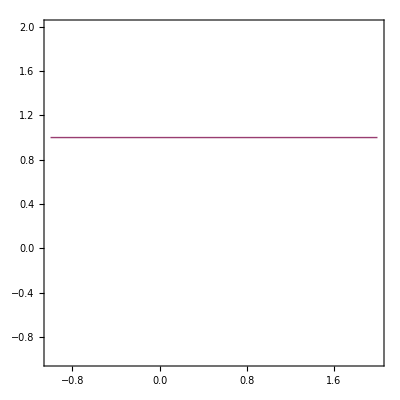

```mathematica
ContourPlot[{y==-2,x==1,y==8,x==3},{y,-1,2},{x,-1,2}]
```

```mathematica
{∫_1^3 (∫_-2^8 (x+2y)ⅆy)ⅆx,Rationalize[∫_-2^8 (∫_1^3 (x+2y)ⅆx)ⅆy]}
```

{160,160}

```mathematica
ContourPlot[{y==-1,x==0,y==16,x==8},{y,1,3},{x,1,3}]
```

-Graphics-

```mathematica
{∫_0^8 (∫_-1^16 1 ⅆy)ⅆx,Rationalize[∫_-1^16 (∫_0^8 1 ⅆx)ⅆy]}
```

{136,136}

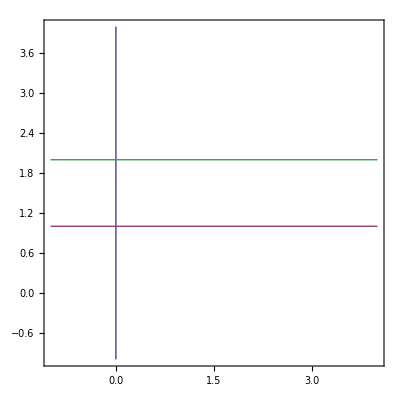

```mathematica
ContourPlot[{y==0,x==1,y==24,x==2},{y,-1,4},{x,-1,4}]
```

```mathematica
{∫_1^2 (∫_0^24 (x^2-y)ⅆy)ⅆx,Rationalize[∫_0^24 (∫_1^2 (x^2-y) ⅆx)ⅆy]}
```

{-232,-232}

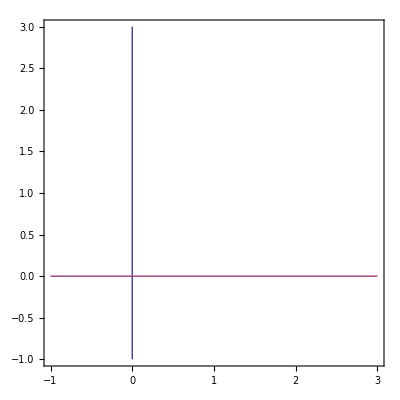

```mathematica
ContourPlot[{y==0,x==0,y==16,x==8},{y,-1,3},{x,-1,3}]
```

```mathematica
{∫_0^8 (∫_0^16 (x^2+y^8)ⅆy)ⅆx,Rationalize[∫_0^16 (∫_0^8 (x^2+y^8) ⅆx)ⅆy]}
```

{549755838464/9,549755838464/9}

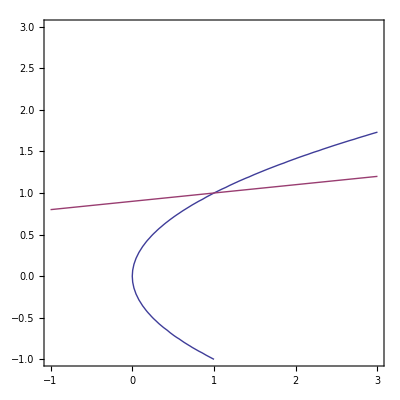

```mathematica
ContourPlot[{y==x^2,y==10x-9},{y,-1,3},{x,-1,3}]
```

```mathematica
{Solve[{y==x^2,y==10x-9},{x,y}]}
```

{{{y→1,x→1},{y→81,x→9}}}

```mathematica
∫_1^9 (∫_(x^2)^(10x-9) ⅆy)ⅆx
```

256/3

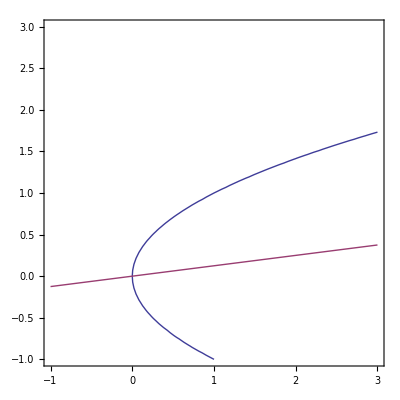

```mathematica
ContourPlot[{y==x^2,y==8x},{y,-1,3},{x,-1,3}]
```

```mathematica
{Solve[{y==x^2,y==8x},{x,y}]}
```

{{{y→0,x→0},{y→64,x→8}}}

```mathematica
∫_0^8 (∫_(x^2)^(8x) (8x*y^2) ⅆy)ⅆx
```

16777216/5

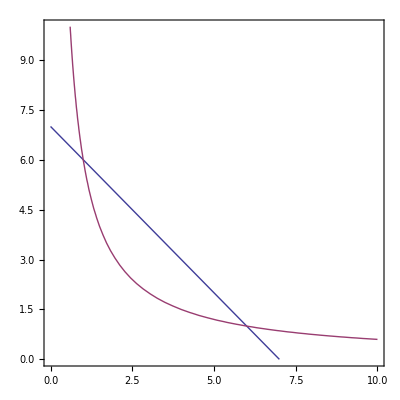

```mathematica
ContourPlot[{x+y==7,x*y==6},{y,0,10},{x,0,10}]
```

```mathematica
{Solve[{x+y==7,x*y==6},{x,y}]}
```

{{{x→1,y→6},{x→6,y→1}}}

```mathematica
∫_1^6 (∫_(7-x)^(6/x) (x)^8 ⅆy)ⅆx
```

-19147625/36

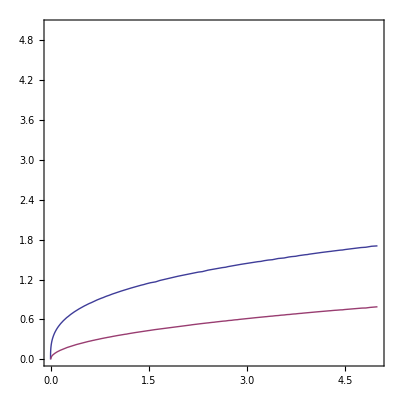

```mathematica
ContourPlot[{y==x^3,y==8 x^2},{y,0,5},{x,0,5}]
```

```mathematica
{Solve[{y==x^3,y==8 x^2},{x,y}]}
```

{{{y→0,x→0},{y→0,x→0},{y→512,x→8}}}

```mathematica
∫_0^8 (∫_(x^3)^(8 x^2) (x^2)ⅆy)ⅆx
```

131072/15

```mathematica
ContourPlot3D[{x==1,y==1,z==0,x==2,y==3,z==8},{x,0,8},{y,0,8},{z,0,8}]
```

-Graphics3D-

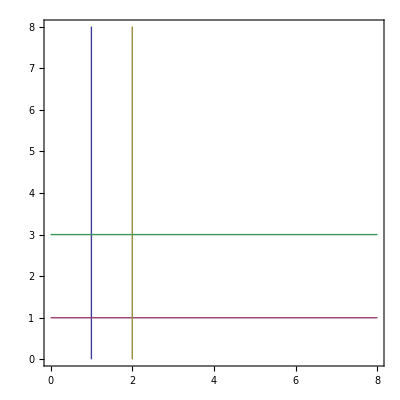

```mathematica
ContourPlot[{x==1,y==1,x==2,y==3},{x,0,8},{y,0,8}]
```

```mathematica
∫_1^2 (∫_1^3 (∫_0^8 (2*x+z)ⅆz)ⅆy)ⅆx
```

112

```mathematica
ContourPlot3D[{x==2,y==1,z==0,x==3,y==2,z==8},{x,0,7},{y,0,7},{z,0,7}]
```

-Graphics3D-

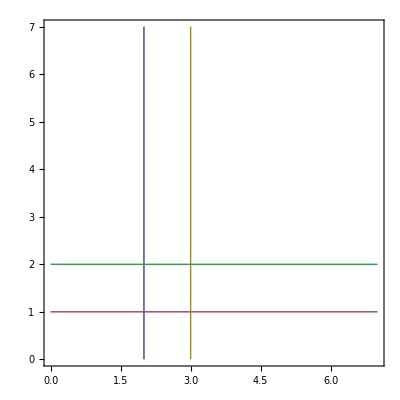

```mathematica
ContourPlot[{x==2,y==1,x==3,y==2},{x,0,7},{y,0,7}]
```

```mathematica
∫_2^3 (∫_1^2 (∫_0^8 y^8 ⅆz)ⅆy)ⅆx
```

4088/9

```mathematica
ContourPlot3D[{x==0,y==0,z==0,x==8,y==16,z==8},{x,0,3},{y,0,3},{z,0,3}]
```

-Graphics3D-

```mathematica
ContourPlot[{x==0,y==0,x==8,y==16},{x,0,3},{y,0,3}]
```

-Graphics-

```mathematica
∫_0^8 (∫_0^16 (∫_0^8 (y+z)ⅆz)ⅆy)ⅆx
```

12288

```mathematica
ContourPlot3D[{x+y+z==8,x==0,y==0,z==0},{x,0,4},{y,0,4},{z,0,4}]
```

-Graphics3D-

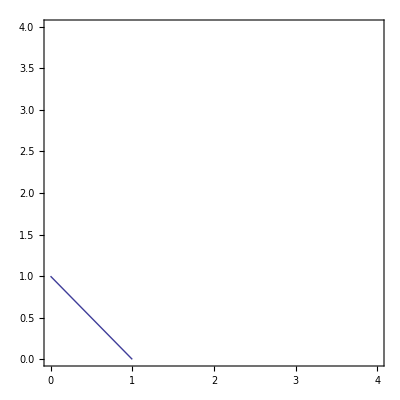

```mathematica
ContourPlot[{x+y==1,x==0,y==0},{x,0,4},{y,0,4}]
```

```mathematica
∫_0^1 (∫_0^(1-x) (∫_0^(1-x-y) 1 ⅆz)ⅆy)ⅆx
```

1/6

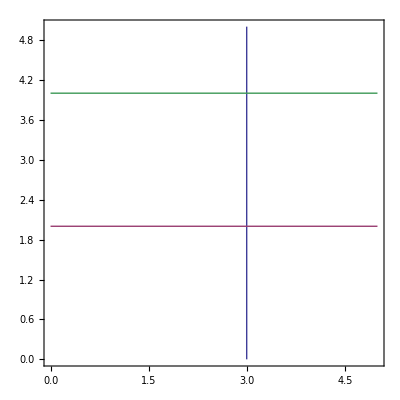

```mathematica
ContourPlot[{y==3,x==2,y==9,x==4},{y,0,5},{x,0,5}]
```

```mathematica
{∫_2^4 (∫_3^9 (2x+3y)ⅆy)ⅆx,Rationalize[∫_3^9 (∫_2^4 (2x+3y)ⅆx)ⅆy]}
```

{288,288}

```mathematica
ContourPlot3D[{x==3,y==1,z==1,x==4,y==6,z==8},{x,0,3},{y,0,3},{z,0,3}]
```

-Graphics3D-

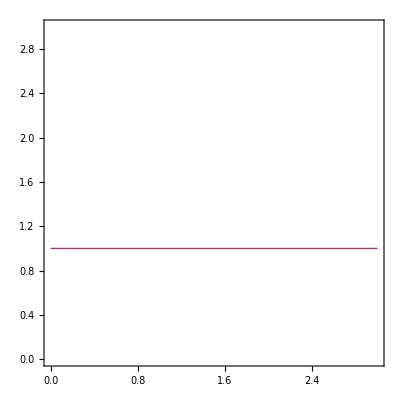

```mathematica
ContourPlot[{x==3,y==1,x==4,y==6},{x,0,3},{y,0,3}]
```

```mathematica
∫_3^4 (∫_1^6 (∫_1^8 (4*x+2(z^8))ⅆz)ⅆy)ⅆx
```

1342181680/9